## Data Preparation

```mathematica
SetDirectory@NotebookDirectory[];
<< "fruit fly functions.wl"
```

C:\Users\nchil\Downloads\Research\Chiles_Bloom_Filter

#### HIV

```mathematica
hiv=Import["HIV.csv","Dataset",HeaderLines->1];
hivtable=Normal@hiv[GroupBy["HIV_active"],All,"smiles"];
actHIVmol=Molecule/@hivtable[1];
inactHIVmol=Molecule/@hivtable[0][[1;;1487]];
(* 1487 examples each of active/inactive *)
actHIV=SparseArray/@FeatureExtract[actHIVmol,"MoleculeExtendedConnectivity"] ;(* bit vectors locally*)
inactHIV=SparseArray/@FeatureExtract[inactHIVmol,"MoleculeExtendedConnectivity"] ;
```

#### Mu

```mathematica
actMu=Get["mu_active.mx"];
inactMu=Get["mu_inactive.mx"];
```

#### Tox

```mathematica
d2=Import["tox21.csv.gz","Dataset",HeaderLines->1];
nrar=Normal@d2[GroupBy["NR-AR"],All,"smiles"];
t=Molecule/@nrar[[3]];
nont=Molecule/@nrar[[1]];
tox=SparseArray/@FeatureExtract[t,"MoleculeExtendedConnectivity"];
nontox=SparseArray/@FeatureExtract[nont,"MoleculeExtendedConnectivity"];
```

#### HIV Dataset

```mathematica
SeedRandom[2000];
```

```mathematica
fly1={pos[actHIV,inactHIV][20,500,50],neg[actHIV,inactHIV][20,500,50]};
```

```mathematica
dt1=classStats["DecisionTree",actHIV,inactHIV][20,500,50];
rf1=classStats["RandomForest",actHIV,inactHIV][20,500,50];
lr1=classStats["LogisticRegression",actHIV,inactHIV][20,500,50];
nn1=classStats["NearestNeighbors",actHIV,inactHIV][20,500,50];
```

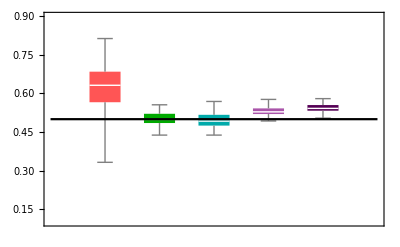

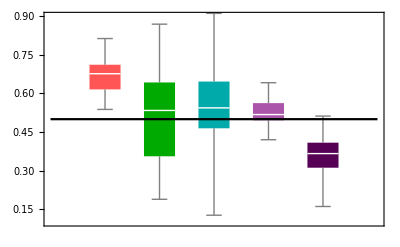

```mathematica
accHIV=accChart[fly1,dt1,rf1,lr1,nn1];
recHIV=recChart[fly1,dt1,rf1,lr1,nn1];
a1=Show[accHIV,horiz]
a2=Show[recHIV,horiz]
```

F1 score might be a better measure of performance across classifiers...

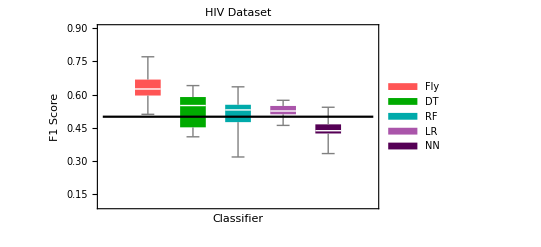

```mathematica
(* a3=Show[BoxWhiskerChart[
F1HIV,
ChartStyle->{Lighter[Red],Darker[Green],Darker[Cyan],Lighter[Purple],Darker[Purple]},
PlotLabel->"HIV Dataset",
LabelStyle->{FontSize->14,FontFamily->"Times",Black,Bold},
PlotRange->{0.1,0.9},
ChartLegends->Placed[{"Fly","DT","RF","LR","NN"},Right],
FrameLabel->{"Classifier","F1 Score"}],horiz] *)
```

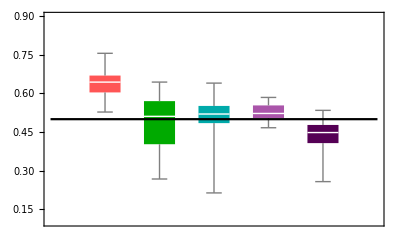

```mathematica
F1HIV=F1List[fly1,dt1,rf1,lr1,nn1];
F1GraphHIV=F1Chart[F1HIV];
a3=Show[F1GraphHIV,horiz]
```

```mathematica
(* Comparing run times -- code back in if this data is desired *)
(* bloomTime=Timing[{outHIVpos[20,100,10],outHIVneg[20,100,10]}];
lrTime=Timing[alllr[20,100,10]];
bloomTime2=Timing[{outHIVpos[20,500,20],outHIVneg[20,500,20]}];
lrTime2=Timing[alllr[20,500,20]]; *)
```

```mathematica
rowHIV=GraphicsRow[{a1,a2,a3}];
```

#### Mu Dataset

```mathematica
SeedRandom[2000];
```

```mathematica
fly2={pos[actMu,inactMu][20,500,50],neg[actMu,inactMu][20,500,50]};
```

```mathematica
dt2=classStats["DecisionTree",actMu,inactMu][20,500,50];
rf2=classStats["RandomForest",actMu,inactMu][20,500,50];
lr2=classStats["LogisticRegression",actMu,inactMu][20,500,50];
nn2=classStats["NearestNeighbors",actMu,inactMu][20,500,50];
```

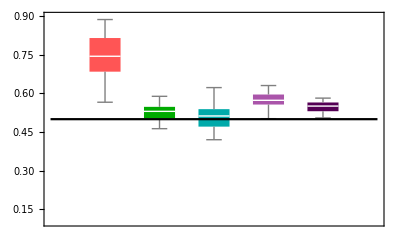

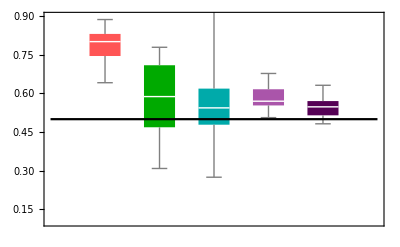

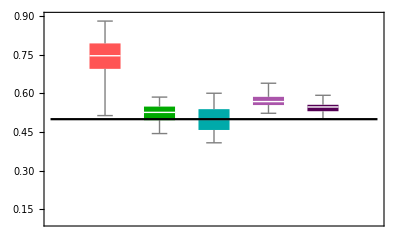

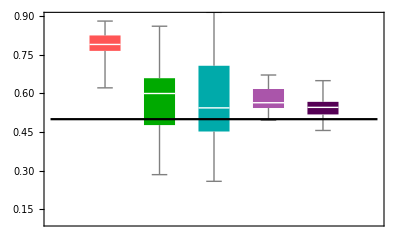

```mathematica
accMu=accChart[fly2,dt2,rf2,lr2,nn2];
recMu=recChart[fly2,dt2,rf2,lr2,nn2];
b1=Show[accMu,horiz]
b2=Show[recMu,horiz]
```

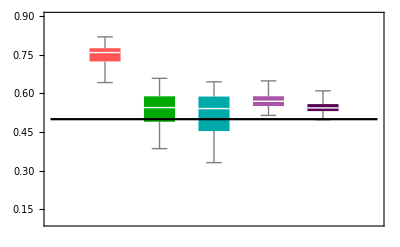

```mathematica
F1Mu=F1List[fly2,dt2,rf2,lr2,nn2];
F1GraphMu=F1Chart[F1Mu];
b3=Show[F1GraphMu,horiz]
```

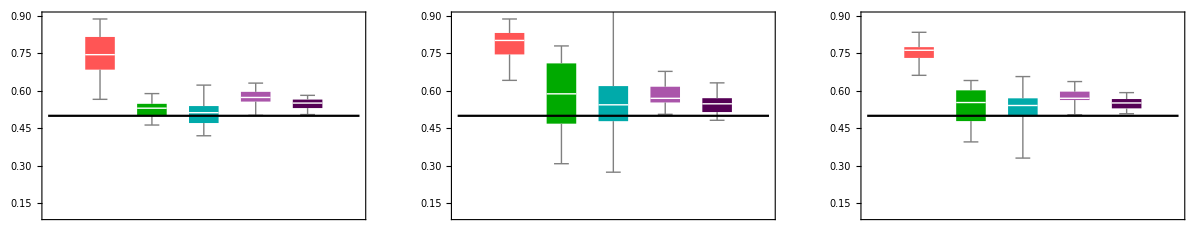

```mathematica
rowMu=GraphicsRow[{b1,b2,b3}];
```

#### Tox Dataset

```mathematica
SeedRandom[2000];
```

```mathematica
fly3={pos[tox,nontox][20,200,50],neg[tox,nontox][20,200,50]};
```

```mathematica
dt3=classStats["DecisionTree",tox,nontox][20,200,50];
rf3=classStats["RandomForest",tox,nontox][20,200,50];
lr3=classStats["LogisticRegression",tox,nontox][20,200,50];
nn3=classStats["NearestNeighbors",tox,nontox][20,200,50];
```

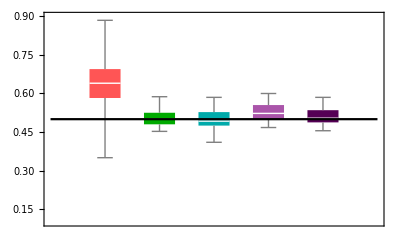

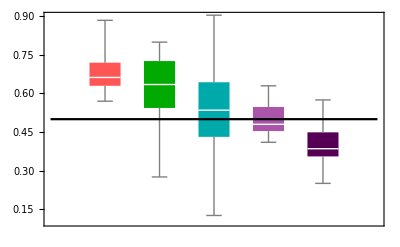

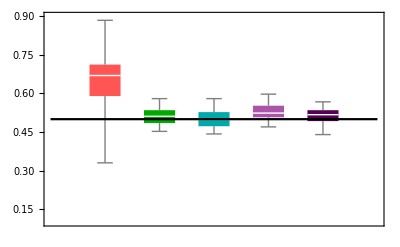

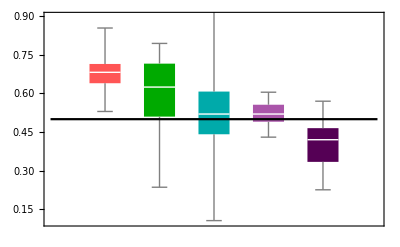

```mathematica
accTox=accChart[fly3,dt3,rf3,lr3,nn3];
recTox=recChart[fly3,dt3,rf3,lr3,nn3];
c1=Show[accTox,horiz]
c2=Show[recTox,horiz]
```

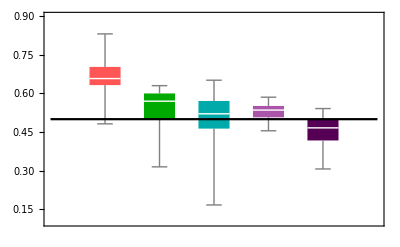

```mathematica
F1Tox=F1List[fly3,dt3,rf3,lr3,nn3];
F1GraphTox=F1Chart[F1Tox];
c3=Show[F1GraphTox,horiz]
```

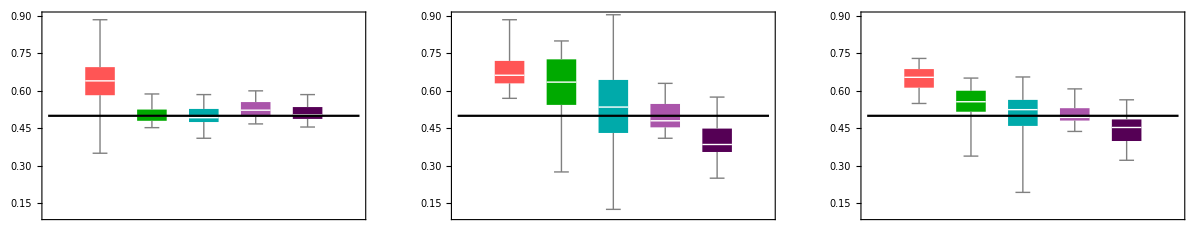

```mathematica
rowTox=GraphicsRow[{c1,c2,c3}];
```

Takeaway: The Bloom filter model consistently performs as well as traditional classifiers under low-data constraints. It also benefits from quick and simple computation.
This may not provide an alternative to accepted classifying methods in its current state but this shows promise for other applications when training data is sparse and predictions must be made with low processing power.

```mathematica
plots={{a1,a2,a3},{b1,b2,b3},{c1,c2,c3}};
xlabels=Text[Style[#,FontFamily->"Times",Large]]&/@{"","Accuracy","Recall","F1 Score"};
ylabels=Text[Style[#,FontFamily->"Times",Large]]&/@{"HIV Dataset","Mu Dataset","Tox Dataset"};
Grid[Join[{xlabels},Transpose[Join[{ylabels},Transpose[plots]]]],Spacings->{2,1}]
```

| Accuracy | Recall | F1 Score
HIV Dataset | -Graphics- | -Graphics- | -Graphics-
Mu Dataset | -Graphics- | -Graphics- | -Graphics-
Tox Dataset | -Graphics- | -Graphics- | -Graphics-